## Use the file in Import Sector

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\Prajwal\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\Prajwal\Dropbox\nEDM\Pictures

(SysDir) System Directory: C:\Users\Prajwal\Dropbox\nEDM\system

Runs in the list: runNum = {12697}

#Runs in the list: runn = 1

622

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

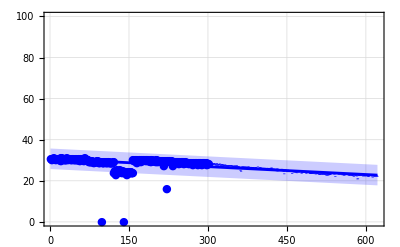
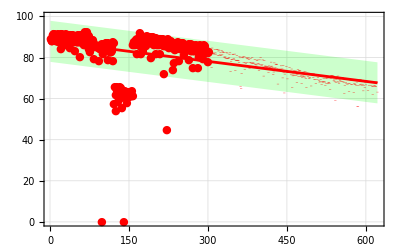

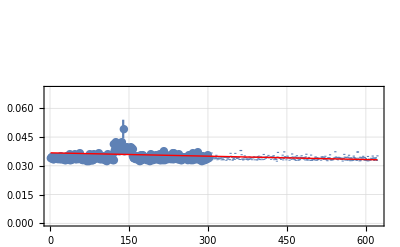

| Estimate | Standard Error | t-Statistic | P-Value
aa | 0.0367756 | 0.000962577 | 38.2053 | 4.43324×10^-165
bb | -5.82646×10^-6 | 2.67721×10^-6 | -2.17632 | 0.0299082

{0.000962577,2.67721×10^-6}

| DF | SS | MS
Model | 2 | 0.760919 | 0.380459
Error | 620 | 0.089114 | 0.000143732
Uncorrected Total | 622 | 0.850033 | 
Corrected Total | 621 | 0.0897947 |

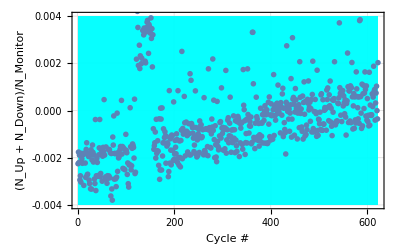

```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"]];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",ScrDir="C:\\Users\\Prajwal\\Dropbox\\Scratch"];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\Pictures"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\system"];
];
Print["Runs in the list: runNum = ",runNum={12697}]
Print["#Runs in the list: runn = ",runn=Dimensions[runNum][[1]]];
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
histbeg=100;histlast=1400;icycle=25;ChNum=4;binw=10;
runi=1;
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_Meta5.edm"],metaStructure2];
begCy=1;
maxCy=Dimensions[data][[1]]
ptud=Table[{data[[k]][[2]],{data[[k]][[27]]+data[[k]][[28]],Sqrt[data[[k]][[27]]+data[[k]][[28]]]}/1000},{k,begCy,maxCy}];
ptmon=Table[{data[[k]][[2]],{data[[k]][[30]],Sqrt[data[[k]][[30]]]}/10000},{k,begCy,maxCy}];
ptudmon=Table[{data[[k]][[2]],{(data[[k]][[27]]+data[[k]][[28]])/data[[k]][[30]],((Sqrt[data[[k]][[27]]+data[[k]][[28]]])/data[[k]][[30]]+(Sqrt[data[[k]][[30]]]*(data[[k]][[27]]+data[[k]][[28]])/data[[k]][[30]]^2))}},{k,begCy,maxCy}];
ftud=Table[{data[[k]][[2]],(data[[k]][[27]]+data[[k]][[28]])/1000},{k,begCy,maxCy}];
ftmon=Table[{data[[k]][[2]],(data[[k]][[30]])/10000},{k,begCy,maxCy}];
ftudmon=Table[{data[[k]][[2]],(data[[k]][[27]]+data[[k]][[28]])/data[[k]][[30]]},{k,begCy,maxCy}];
nlmud=NonlinearModelFit[ftud,aa+bb Exp[-cc xx],{{aa,1},{bb,10},{cc,.1}},xx];
nlmmon=NonlinearModelFit[ftmon,aa+bb Exp[-cc xx],{{aa,1},{bb,10},{cc,.1}},xx];
nlmudmon=NonlinearModelFit[ftudmon,aa+bb xx,{{aa,1},{bb,10}},xx];
pt1=Show[{Plot[{nlmud[xx],nlmud[xx]+5,nlmud[xx]-5},{xx,begCy,maxCy},Filling->{2->{3}},FillingStyle->{Opacity[.5],Blue},PlotRange->{{begCy,maxCy},{0,100}},PlotStyle->{{Blue,Thickness[.005]},None,None},GridLines->Automatic,Frame->{True,True,False,False},FrameStyle->{{Blue,Thickness[.005]},
{Blue,Thickness[.005]},None,None},FrameLabel->{"Cycle #","N_Up+N_Down (×1k)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000}],
EDAListPlot[ptud,PlotRange->{{begCy,maxCy},{0,100}},PlotStyle->{Blue},GridLines->Automatic,Frame->{True,True,False,False},FrameStyle->{{Blue,Thickness[.005]},{Blue,Thickness[.005]},None,None},FrameLabel->{"Cycle #","N_Up+N_Down (×1k)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotMarkers->{Automatic, Medium}]
},ImagePadding->125];
pt2=Show[{
Plot[{nlmmon[xx],nlmmon[xx]+10,nlmmon[xx]-10},{xx,begCy,maxCy},Filling->{2->{3}},FillingStyle->{Opacity[.5],Green},PlotRange->{{begCy,maxCy},{0,100}},PlotStyle->{{Red,Thickness[.005]},None,None},GridLines->Automatic,Frame->{False,False,True,True},FrameStyle->{None,None,{Red,Thickness[.005]},{Red,Thickness[.005]}},FrameLabel->{"","","",Rotate["N_Monitor (×10k)",180Degree]},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000}],
EDAListPlot[ptmon,PlotRange->{{begCy,maxCy},{0,100}},PlotStyle->{Red},GridLines->Automatic,Frame->{False,False,True,True},FrameStyle->{None,None,{Red,Thickness[.005]},{Red,Thickness[.005]}},FrameLabel->{"","","",Rotate["N_Monitor (×10k)",180Degree]},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotMarkers->{Automatic, Medium}]
},ImagePadding->125];
pt3=Overlay[{pt1,pt2},ImageSize->1200]
pt4=Show[{
EDAListPlot[ptudmon,PlotRange->{{begCy,maxCy},{0,0.07}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"Cycle #","(N_Up + N_Down)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000},PlotMarkers->{Automatic, Medium}],
Plot[nlmudmon[x],{x,begCy,maxCy},PlotRange->{{begCy,maxCy},{0,0.07}},PlotStyle->{Red,Thick},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"x","y"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000}]
},ImagePadding->125]
nlmudmon["ParameterTable"]
nlmudmon["ParameterErrors"]
nlmudmon["ANOVATable"]
ptudmonres=Table[{k-1+begCy,nlmudmon["FitResiduals"][[k]]},{k,1,maxCy-begCy+1}];
sdptudmonres=StandardDeviation[ptudmonres[[;;,2]]];
pt5=Show[{
Plot[{sdptudmonres,-sdptudmonres,
2sdptudmonres,-2sdptudmonres,
3sdptudmonres,-3sdptudmonres,
4sdptudmonres,-4sdptudmonres,
5sdptudmonres,-5sdptudmonres
},{x,begCy,maxCy},Filling->{{1->{2}},{3->{4}},{5->{6}},{7->{8}},{9->{10}}},FillingStyle->Opacity[.5,Cyan],PlotRange->{{begCy,maxCy},{-.004,.004}},PlotStyle->{None,None},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"Cycle #","(N_Up + N_Down)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{27,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000}],
EDAListPlot[ptudmonres,PlotRange->{{begCy,maxCy},{-.005,.005}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"Cycle #","[(N_Up + N_Down)/N_Monitor]Residual"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{27,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000},PlotMarkers->{Red, Medium}]
},ImagePadding->125]
```

```mathematica
StandardDeviation[ptudmonres[[;;,2]]]
nlmudmon["ParameterErrors"][[1]]
```

0.0119792

0.000962577

```mathematica
Mean[ftudmon[[;;,2]]]
```

0.0349607

```mathematica
cnt={};
excllmt=.04;
For[i=begCy+2,i≤maxCy-2,i++,
If[(
(
Abs[nlmudmon["FitResiduals"][[i-begCy+1]]]>5sdptudmonres
)||
(
data[[i]][[30]]<500000;
)||
(
(data[[i]][[27]]+data[[i]][[28]])<5000;
)||
(
(
(Abs[data[[i]][[30]]-data[[i-2]][[30]]]>excllmt*data[[i]][[30]])&&
(Abs[data[[i+2]][[30]]-data[[i]][[30]]]>excllmt*data[[i]][[30]])
)&&
(
(Abs[data[[i]][[30]]-data[[i-1]][[30]]]>excllmt*data[[i]][[30]])&&
(Abs[data[[i+1]][[30]]-data[[i]][[30]]]>excllmt*data[[i]][[30]])
)
)||
(
Abs[ftudmon[[i]][[2]]-Mean[ftudmon[[;;,2]]]]>excllmt*Mean[ftudmon[[;;,2]]]
)
),
cnt=AppendTo[cnt,i];
];
];
bddata=Part[data,cnt];
gddata=DeleteCases[data,Alternatives@@bddata];
maxCy2=begCy+Dimensions[gddata][[1]]-1
gddata[[maxCy2]][[2]]
{gddata[[begCy]][[2]],gddata[[maxCy2]][[2]]}
```

364

622.

{1.,622.}

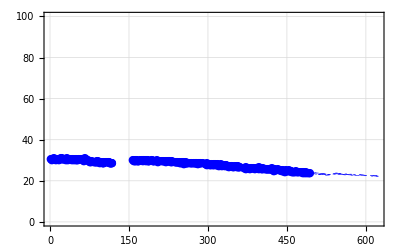
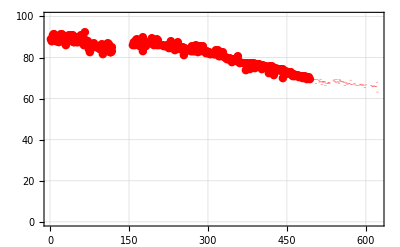

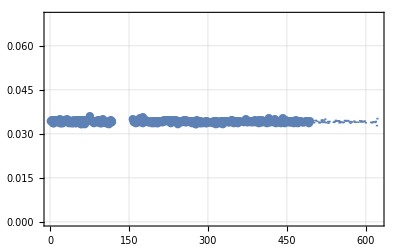

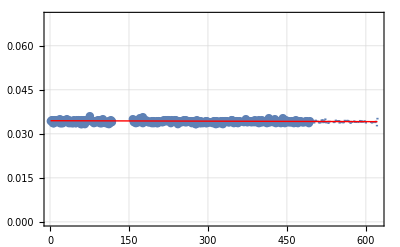

| Estimate | Standard Error | t-Statistic | P-Value
aa | 0.0344824 | 0.0000415161 | 830.581 | 7.784225016224×10^-596
bb | -5.23161×10^-7 | 1.1926×10^-7 | -4.38672 | 0.0000151111

{0.0000415161,1.1926×10^-7}

| DF | SS | MS
Model | 2 | 0.428899 | 0.21445
Error | 362 | 0.0000599017 | 1.65474×10^-7
Uncorrected Total | 364 | 0.428959 | 
Corrected Total | 363 | 0.000063086 |

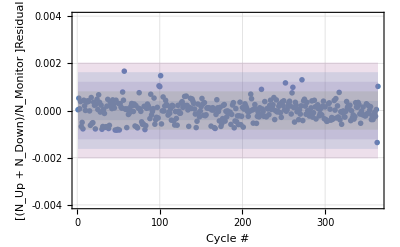

```mathematica
gdptud=Table[{gddata[[k]][[2]],{gddata[[k]][[27]]+gddata[[k]][[28]],Sqrt[gddata[[k]][[27]]+gddata[[k]][[28]]]}/1000},{k,begCy,maxCy2}];
gdptmon=Table[{gddata[[k]][[2]],{gddata[[k]][[30]],Sqrt[gddata[[k]][[30]]]}/10000},{k,begCy,maxCy2}];
gdptudmon=Table[{gddata[[k]][[2]],{(gddata[[k]][[27]]+gddata[[k]][[28]])/gddata[[k]][[30]],((Sqrt[gddata[[k]][[27]]+gddata[[k]][[28]]])/gddata[[k]][[30]]+(Sqrt[gddata[[k]][[30]]]*(gddata[[k]][[27]]+gddata[[k]][[28]])/gddata[[k]][[30]]^2))}},{k,begCy,maxCy2}];
gdftudmon=Table[{gddata[[k]][[2]],(gddata[[k]][[27]]+gddata[[k]][[28]])/gddata[[k]][[30]]},{k,begCy,maxCy2}];
gdpt1=EDAListPlot[gdptud,PlotRange->{{gddata[[begCy]][[2]],gddata[[maxCy2]][[2]]},{0,100}},ImagePadding->125,PlotStyle->{Blue},GridLines->Automatic,Frame->{True,True,False,False},FrameStyle->{{Blue,Thickness[.005]},{Blue,Thickness[.005]},None,None},FrameLabel->{"Cycle #","N_Up+N_Down (×1k)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotMarkers->{Automatic, Medium}];
gdpt2=EDAListPlot[gdptmon,PlotRange->{{gddata[[begCy]][[2]],gddata[[maxCy2]][[2]]},{0,100}},ImagePadding->125,PlotStyle->{Red},GridLines->Automatic,Frame->{False,False,True,True},FrameStyle->{None,None,{Red,Thickness[.005]},{Red,Thickness[.005]}},FrameLabel->{"","","",Rotate["N_Monitor (×10k)",180Degree]},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotMarkers->{Automatic, Medium}];
Overlay[{gdpt1,gdpt2}]
EDAListPlot[gdptudmon,PlotRange->{{gddata[[begCy]][[2]],gddata[[maxCy2]][[2]]},{0,0.07}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"Cycle #","(N_Up + N_Down)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000},PlotMarkers->{Automatic, Medium}]
gdnlmudmon=NonlinearModelFit[gdftudmon,aa+bb xx,{{aa,1},{bb,10}},xx];
pt4=Show[{
EDAListPlot[gdptudmon,PlotRange->{{gddata[[begCy]][[2]],gddata[[maxCy2]][[2]]},{0,0.07}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"Cycle #","(N_Up + N_Down)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000},PlotMarkers->{Automatic, Medium}],
Plot[gdnlmudmon[x],{x,gddata[[begCy]][[2]],gddata[[maxCy2]][[2]]},PlotRange->{{gddata[[begCy]][[2]],gddata[[maxCy2]][[2]]},{0,0.07}},PlotStyle->{Red,Thick},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"x","y"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000}]
},ImagePadding->125]
gdnlmudmon["ParameterTable"]
gdnlmudmon["ParameterErrors"]
gdnlmudmon["ANOVATable"]
gdptudmonres=Table[{k-1+begCy,gdnlmudmon["FitResiduals"][[k]]},{k,1,maxCy2-begCy+1}];
sdgdptudmonres=StandardDeviation[gdptudmonres[[;;,2]]];
pt5=Show[{
EDAListPlot[gdptudmonres,PlotRange->{{begCy,maxCy2},{-.004,.004}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"Cycle #","[(N_Up + N_Down)/N_Monitor ]Residual"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000},PlotMarkers->{Automatic, Medium}],
Plot[{sdgdptudmonres,-sdgdptudmonres,
2sdgdptudmonres,-2sdgdptudmonres,
3sdgdptudmonres,-3sdgdptudmonres,
4sdgdptudmonres,-4sdgdptudmonres,
5sdgdptudmonres,-5sdgdptudmonres
},{x,begCy,maxCy2},Filling->{{1->{2}},{3->{4}},{5->{6}},{7->{8}},{9->{10}}},PlotRange->Automatic,PlotStyle->{None,None},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"Cycle #","(N_Up + N_Down)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000}]
},ImagePadding->125]
```

```mathematica
runi=1;
Export[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_Meta5-2.dat"],gddata]
```

C:\Users\Prajwal\Dropbox\nEDM\rawdata\012697\012697_Meta5-2.dat